ω at surface: 10

ω at infinity: 8.10093

Modification factor: 0.575998

Time elapsed: 0.031915

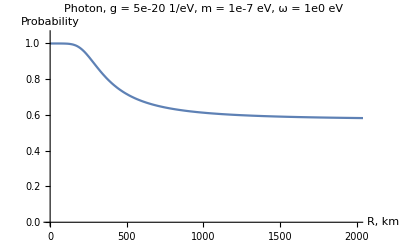

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

(*Параметры АЛП*)
ω0=10^(1);
g=6*10^(-20);
m=10^(-8);

(*Конфигурация поля*)
angle = Pi/6;
BSurf = 10^14;
R0 = 12;
period =3;

(*Размер области, должен быть равен радиусу*)
startingPoint = R0;

(*Радиус светового цилиндра*)
(*upperLimit=47713*period;*)
upperLimit:=300*R0;

(*Значения поля (диполь)*)
bRep:={bRad->BSurf*Cos[angle]*(R0/(x+startingPoint))^3,
	bTheta->0.5*BSurf*Sin[angle]*(R0/(x+startingPoint))^3,
	bPhi->0};

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(4.134/startingPoint))/(1-(4.134/(x+startingPoint)))];


(*Без красного смещения*)
(*ω:=ω0;*)

(*Элементы матрицы М*)
deltaMTheta:=5.0*10^7*bTheta*g;
deltaMPhi:=5.0*10^7*bPhi*g;

deltaMass:=2.5*10^9*m^2*(1/ω);

deltaPlasma:=3.1*10^(-12)*(bRad*Cos[angle]-bTheta*Sin[angle])*(1/period)*(1/ω);

deltaCEDTheta:=-4.5*10^(-22)*ω*bTheta^2;
deltaCEDPhi:=-4.5*10^(-22)*ω*bPhi^2;

(*Матрица М*)
mat:={{deltaPlasma+deltaCEDTheta,0,deltaMTheta},
	{0,deltaPlasma+deltaCEDPhi,deltaMPhi},
	{deltaMTheta,deltaMPhi,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
r[x_]:={{r11[x],r12[x],r13[x]},{r21[x],r22[x],r23[x]},{r31[x],r32[x],r33[x]}};

(*Список начальных условий*)r0={{r11[0]==1,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==0,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};

(*Решаем систему*)
eqs=NDSolve[Join[{ⅈ r'[x]==r[x].mat-mat.r[x]},r0],{r11[x],r22[x],r33[x]},{x,0,upperLimit}, MaxSteps->10^8, AccuracyGoal->5];

Print["ω at surface: ",ω0];
Print["ω at infinity: ",ω/.x->(upperLimit-1)];
Print["Modification factor: ",Re[r11[x]+r22[x]/.First[eqs]/.x->(upperLimit-1)]];
Print["Time elapsed: ",AbsoluteTime[]-time];

p1=Plot[Re[Evaluate[{r11[x]+r22[x]}/.eqs]],{x,0,upperLimit},PlotRange->{{0,2000},{0.0,1.05}},PlotLabel->"Photon, g = 5e-20 1/eV, m = 1e-7 eV, ω = 1e0 eV", AxesLabel->{"R, km","Probability"}]
```